```mathematica
Avg=33
dt={34,15,7,29,47,30,41,61}
D1=0.2321
D2=0.2151
D3=0.2041
P1={12,2,5,5,11,7,9,17}
P2={8,10,15,31,6,1,3,9}
P3={8,4,8,16,12,7,9,15}
FindFit[dt,Avg* ⅇ^Sin[p+t w] ((C1 P1[[t]])/Log[1+D1]+(C2 P2[[t]])/Log[1+D2]+(C3  P3[[t]])/Log[1+D3]+(C4 P4[[t]])/Log[1+D4]+(C5  P5[[t]])/Log[1+D5]),{p,w,C1,C2,C3,C4,C5},t]
```

33

{34,15,7,29,47,30,41,61}

0.2321

0.2151

0.2041

{12,2,5,5,11,7,9,17}

{8,10,15,31,6,1,3,9}

{8,4,8,16,12,7,9,15}

Part::pkspec1: The expression t cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{p→2.86045,w→0.811308,C1→0.0402312,C2→0.0161172,C3→-0.0287886}

Part::pkspec1: The expression 1.00014 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

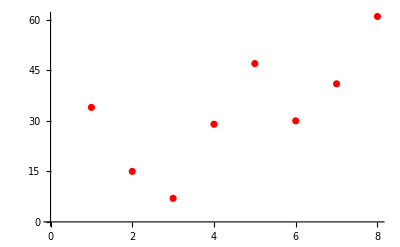

```mathematica
Show[ListPlot[dt,PlotStyle->Red],Plot[Avg ⅇ^Sin[p+t w] ((C1 P1⟦t⟧)/Log[1+D1]+(C2 P2⟦t⟧)/Log[1+D2]+(C3 P3⟦t⟧)/Log[1+D3])/.{p->2.8604548193592545,w->0.811307935970819,C1->0.04023122465662978,C2->0.016117209010432974,C3->-0.028788597768872},{t,1,8}]]
```